```mathematica
word = "bello";
```

```mathematica
dict = ImportString[Import["/Volumes/Space/elan/word_dicts/"<>word<>".txt"],"Table"];
```

```mathematica
TableForm[Table[dict[[n,-4;;-1]],{n,1,Length[dict]}],TableHeadings->{Table[dict[[n,1]],{n,1,Length[dict]}],{"pre-1920","1920-1950","1950-2000","post-2000"}}]
```

| pre-1920 | 1920-1950 | 1950-2000 | post-2000
NNP | 832 | 492 | 279 | 13
UH | 42 | 0 | 2 | 0
IN | 1 | 0 | 0 | 0
FW | 599 | 1 | 1 | 0

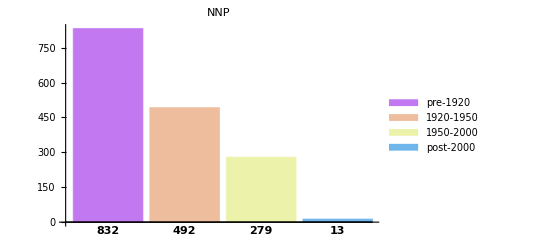
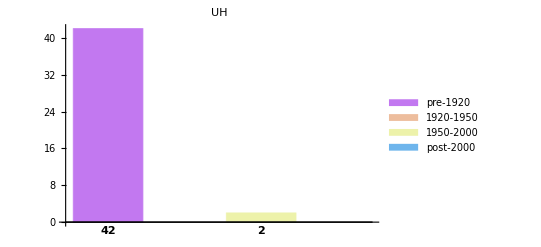
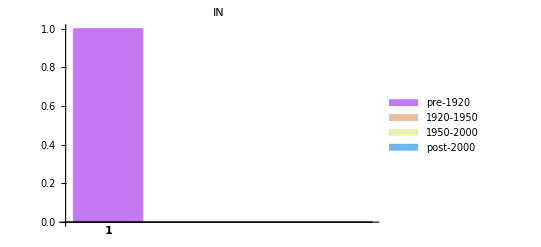
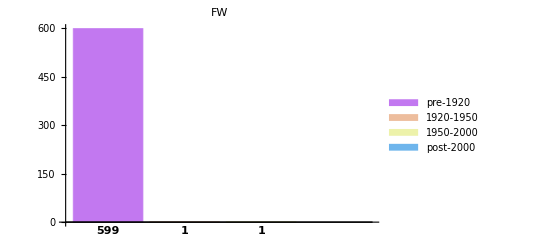

```mathematica
Table[BarChart[dict[[n,-4;;-1]],PlotLabel->dict[[n,1]],ChartLegends->{"pre-1920","1920-1950","1950-2000","post-2000"},ChartStyle->"Pastel",ChartLabels->Placed[Table[dict[[n,m]],{m,-4,-1}],Below,Style[#,Bold]&]],{n,1,Length[dict]}]
```

```mathematica
words = ImportString[Import["/Volumes/Space/elan/total_word_counts.txt"],"Table"]
```

$Aborted

```mathematica
data = Import["/tmp/sw1.csv"];
```

```mathematica
data⟦1;;10⟧
```

{{is ,2475466},{was ,1873806},{are ,1329087},{be ,1188152},{made ,1113218},{were ,965667},{have ,856111},{had ,797247},{found ,671136},{see ,651943}}

```mathematica
Exp[Log[3*^4]/100.]
```

1.10859

```mathematica
Table[ data⟦i⟧,{i,Table[Ceiling[1.1085906529925522^n],{n,10,99}]}]//TableForm
```

are  | 1329087
be  | 1188152
be  | 1188152
be  | 1188152
made  | 1113218
made  | 1113218
were  | 965667
were  | 965667
have  | 856111
had  | 797247
had  | 797247
found  | 671136
see  | 651943
said  | 637484
been  | 615676
used  | 551582
come  | 523831
make  | 507974
put  | 488666
given  | 459395
has  | 433981
use  | 423473
brought  | 415237
give  | 378676
took  | 358145
form  | 334869
man  | 323450
know  | 302708
place  | 282665
say  | 275255
turned  | 260321
system  | 242214
obtained  | 225892
appear  | 217261
produced  | 206564
appeared  | 199810
point  | 186937
name  | 176807
laid  | 172294
run  | 162907
developed  | 156299
help  | 147691
letter  | 140682
believe  | 129300
years  | 122534
play  | 118241
accepted  | 110395
serve  | 104891
prevent  | 99628
maintained  | 93693
stopped  | 88272
laws  | 84546
acquired  | 79513
shot  | 73637
knows  | 68369
fail  | 63268
member  | 59515
progress  | 55527
survey  | 51349
attributed  | 47156
swept  | 42971
explanation  | 39267
placing  | 35801
consciousness  | 32612
withdrawn  | 29599
headed  | 26833
corps  | 24353
logic  | 21984
layers  | 19862
pushing  | 17699
heaven  | 15707
depressed  | 13998
slopes  | 12386
kindled  | 10906
wet  | 9434
meters  | 8232
indicator  | 7131
fuller  | 6166
contingent  | 5304
frenchman  | 4579
knox  | 3942
chlorine  | 3345
lighten  | 2861
hindu  | 2408
salon  | 2020
facies  | 1703
stupor  | 1426
sepoys  | 1183
mechanization  | 979
bello  | 809

```mathematica
Position[data,{"eikonal ",_}]
```

{{292272}}

```mathematica
data⟦3⟧
```

{are ,1329087}

```mathematica
Table[Ceiling[1.14826^n],{n,10,99}]
```

{4,5,6,7,7,8,10,11,13,14,16,19,21,25,28,32,37,42,48,56,64,73,84,96,110,127,146,167,192,220,253,290,333,382,439,504,578,664,762,875,1005,1154,1325,1522,1747,2006,2303,2645,3037,3487,4004,4597,5279,6061,6960,7992,9177,10537,12099,13893,15953,18318,21033,24152,27732,31844,36565,41986,48211,55358,63566,72990,83811,96237,110505,126888,145701,167302,192106,220588,253292,290845,333966,383480,440334,505618,580581,666658,765497,878989}

```mathematica
Length[data]
```

```mathematica
Timing[Do[data[[RandomInteger[{1,10^6}]]],{100}]]
```

```mathematica
{0.00028299999999999999418173746157378901`2.4723863488039144,Null}
```

{0.00028,Null}

```mathematica
WordData[]
```

$Aborted

```mathematica
WordData[];
```

```mathematica
Length[WordData[]]
```

149191